```mathematica
(* Simualting the simple reaction [R] + [S] -> <- [RS] so that
d[R]/dt = - kPlus [R] [S] + kMinus [RS]
d[S]/dt = - kPlus [R] [S] + kMinus [RS]
d[RS]/dt = kPlus [R] [S] - kMinus [RS] *)
kPlus := 0.5; kMinus := 0.2;
initR := 9; initS  := 10;
initRS := 0; endT := 5;
```

{{RS→InterpolatingFunction[{{0., 5.}}, <>]}}

{{R→InterpolatingFunction[{{0., 5.}}, <>]}}

{{S→InterpolatingFunction[{{0., 5.}}, <>]}}

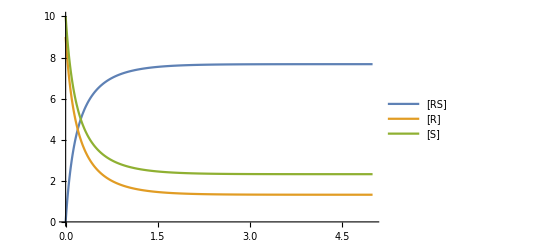

```mathematica
RSvals = NDSolve[{R'[t]==-kPlus*R[t]*S[t] + kMinus*RS[t],S'[t]==-kPlus*R[t]*S[t] + kMinus*RS[t],RS'[t]==kPlus*R[t]*S[t] - kMinus*RS[t],R[0]==initR,S[0]==initS,RS[0]==initRS},RS,{t,0,endT}]
Rvals = NDSolve[{R'[t]==-kPlus*R[t]*S[t] + kMinus*RS[t],S'[t]==-kPlus*R[t]*S[t] + kMinus*RS[t],RS'[t]==kPlus*R[t]*S[t] - kMinus*RS[t],R[0]==initR,S[0]==initS,RS[0]==initRS},R,{t,0,endT}]
Svals = NDSolve[{R'[t]==-kPlus*R[t]*S[t] + kMinus*RS[t],S'[t]==-kPlus*R[t]*S[t] + kMinus*RS[t],RS'[t]==kPlus*R[t]*S[t] - kMinus*RS[t],R[0]==initR,S[0]==initS,RS[0]==initRS},S,{t,0,endT}]
Plot[{Evaluate[RS[t]/.RSvals],Evaluate[R[t]/.Rvals],Evaluate[S[t]/.Svals]},{t,0,endT},PlotLegends->{"[RS]","[R]","[S]"}]
```